```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
pp[f_,n_, 0] := UnitStep[n-1]
pp[f_,n_, k_] := pp[f,n,k]=Sum[ f[j] pp[f,Floor[n/j],k-1],{j,2,n}]
ppa[f_,n_, 0,a_] := UnitStep[n-1]
ppa[f_,n_,1,a_]:=ppa[f,n,1,a]=N[Sum[ f[m],{m,a+1,n}]]
ppa[f_,n_,k_,a_]:=ppa[f,n,k,a]=N[Sum[bin[k,j] f[m]^j ppa[f,Floor[n/(m^j)],k-j, m],{j,1,k},{m,a+1,Floor[n^(1/k)]}]]
pz[f_,n_, z_] := Sum[ bin[ z,k] pp[f,n,k],{k,0,Log[2,n]}]
pza[f_,n_, z_] := Sum[ bin[ z,k] ppa[f,n,k,1],{k,0,Log[2,n]}]
pz2[f_,n_, z_] := Sum[ z^k f[k+1],{k,0,n}]
pzeros[f_,n_]:=List@@NRoots[pz[f,n,z]==0,z][[All,2]]
pzerosa[f_,n_]:=List@@NRoots[pza[f,n,z]==0,z][[All,2]]
pzeros2[f_,n_]:=List@@NRoots[pz2[f,n,z]==0,z][[All,2]]
zeta[0,s_,z_,k_]:=0
zeta[n_, s_, z_, 0] := UnitStep[n-1]
zeta[n_,s_,z_,k_]:=zeta[n,s,z,k]=1+((z+1)/k-1) Sum[j^-s zeta[Floor[n/j],s,z,k+1],{j,2,n}]
dzeta[n_, s_, z_] := zeta[n,s,z,1]-zeta[n-1,s,z,1]
```

```mathematica
lg[n_,k_]:=1-k(Floor[n/k]-Floor[(n-1)/k])
fe[n_] := 1
fx[n_] := n^-s
ff[n_] := N[1/((n-1)!)]
ff2[n_] := N[1/(n!)]
fr[n_] := fs[n-1]
fg[n_] := (-1)^(n-1) 1/((n-1)!)
fh[n_] := (I)^(n-1) 1/((n-1)!)
gg[n_] := gg[n] = D[Cos[x],{x,n}]/.x->0
hh[n_] := hh[n] = D[Cos[x],{x,n-1}]/.x->0
cs[n_] := cs[n] = (D[Cos[x],{x,n-1}]/.x->0)/((n-1)!)
sn[n_] := sn[n] = (D[Sin[x],{x,n-1}]/.x->0)/((n-1)!)
exp[n_] := exp[n] = 1/((n-1)!)
jj[n_] := (-1)^(n+1)/n
fo[n_] := 0; fo[1] := 7; fo[2] := 3; fo[3] := 12; fo[4] := 55; fo[5] := -3+I; fo[6] := -7
```

```mathematica
ff[8]
```

1/5040

```mathematica
Expand[pza[jj,100000,z]]
```

1-0.359995 z+0.0388798 z^2+0.0391955 z^3-0.0401951 z^4+0.0205268 z^5-0.00635971 z^6+0.00122432 z^7-0.000144154 z^8+0.0000101242 z^9-4.1536×10^-7 z^10+8.50103×10^-9 z^11-6.97606×10^-11 z^12+3.37341×10^-12 z^13-1.36292×10^-13 z^14+1.44886×10^-15 z^15-7.04981×10^-18 z^16

```mathematica
Expand[pz[ff,60,0,z]]
```

1+(2931003346949718170578224494139352409419032200378117270318906218274370849923909 z)/3467077963642245893448475493009735158647571919317185813520532373504000000000000+(668802103698132768433689196979 z^2)/884176199373970195454361600000+(573482765 z^3)/6974263296+(11 z^4)/2160+(7 z^5)/240

```mathematica
N[pz[ff,60,0,-1]]
```

0.804729

```mathematica
N[Expand[pz[ff,500,0,z]]]
```

1.+1.22792 z-0.119284 z^2+0.822859 z^3-0.31065 z^4+0.109187 z^5-0.0123753 z^6+0.000501268 z^7+0.000124008 z^8

```mathematica
N[D[Expand[pz[ff,400,0,z]],z]/.z->0]
```

0.78388

```mathematica
pzeros[ff,500,0]
```

{-15.2276,-0.597394,0.0086062-1.44375 ⅈ,0.0086062+1.44375 ⅈ,1.54627-3.01933 ⅈ,1.54627+3.01933 ⅈ,4.33653-4.26038 ⅈ,4.33653+4.26038 ⅈ}

```mathematica
Product[ 1-1/j,{j,pzeros[ff,500,0]}]
```

2.71828+0. ⅈ

```mathematica
Table[ {80 n, N[pz[ff,80 n,0,(2 Pi I)]]},{n,1,40}]//TableForm
```

80 | -301.288+227.97 ⅈ
160 | -138.791-510.916 ⅈ
240 | 284.677-567.874 ⅈ
320 | 604.564+131.935 ⅈ
400 | 206.287-36.9285 ⅈ
480 | 568.929+702.92 ⅈ
560 | 649.614+548.514 ⅈ
640 | -413.519+399.338 ⅈ
720 | -213.391+917.398 ⅈ
800 | 136.375+512.984 ⅈ
880 | -975.691+152.597 ⅈ
960 | -1145.89+121.769 ⅈ
1040 | -1085.99+320.45 ⅈ
1120 | -1044.63+439.849 ⅈ
1200 | -20.4109-309.537 ⅈ
1280 | 9.89149-344.706 ⅈ
1360 | -734.927-682.984 ⅈ
1440 | -1015.82-773.154 ⅈ
1520 | -1009.46-749.508 ⅈ
1600 | -1001.85-228.975 ⅈ
1680 | -988.189-180.024 ⅈ
1760 | 560.751-954.867 ⅈ
1840 | 566.834-941.031 ⅈ
1920 | 739.42-1067.78 ⅈ
2000 | 432.623-1240.57 ⅈ
2080 | 366.752-1281.14 ⅈ
2160 | 119.354-1395.07 ⅈ
2240 | 119.209-1393.71 ⅈ
2320 | -175.583+23.916 ⅈ
2400 | -199.085+16.1965 ⅈ
2480 | -196.683+26.1896 ⅈ
2560 | -195.595+71.2173 ⅈ
2640 | 1208.-399.653 ⅈ
2720 | 1215.95-395.839 ⅈ
2800 | 1215.96-395.801 ⅈ
2880 | 1607.88-588.019 ⅈ
2960 | 1529.4-638.43 ⅈ
3040 | 1521.44-641.391 ⅈ
3120 | 1206.86-1013.91 ⅈ
3200 | 1214.17-1019.19 ⅈ

```mathematica
N[E^(2 Pi I)]
```

1.

```mathematica
Product[ 1+.5/j,{j,pzeros[ff,3200,0]}]
```

-0.0386673-8.67362×10^-19 ⅈ

```mathematica
Table[gg[n],{n,0,10}]
```

{1,0,-1,0,1,0,-1,0,1,0,-1}

```mathematica
Product[ 1-3/j,{j,pzeros[hh,3200,0]}]
```

-50.+0. ⅈ

```mathematica
N[Expand[pz[hh,3200,0,z]]]
```

1.+0.940476 z-3.80278 z^2+3.38611 z^3-1.67361 z^4+0.173611 z^5-0.0236111 z^6-0.000198413 z^7

```mathematica
Table[ {80 n, N[pz[ff,80 n,0,2]]},{n,1,40}]//TableForm
```

80 | 7.38906
160 | 7.38906
240 | 7.38906
320 | 7.38906
400 | 7.38906
480 | 7.38906
560 | 7.38906
640 | 7.38906
720 | 7.38906
800 | 7.38906
880 | 7.38906
960 | 7.38906
1040 | 7.38906
1120 | 7.38906
1200 | 7.38906
1280 | 7.38906
1360 | 7.38906
1440 | 7.38906
1520 | 7.38906
1600 | 7.38906
1680 | 7.38906
1760 | 7.38906
1840 | 7.38906
1920 | 7.38906
2000 | 7.38906
2080 | 7.38906
2160 | 7.38906
2240 | 7.38906
2320 | 7.38906
2400 | 7.38906
2480 | 7.38906
2560 | 7.38906
2640 | 7.38906
2720 | 7.38906
2800 | 7.38906
2880 | 7.38906
2960 | 7.38906
3040 | 7.38906
3120 | 7.38906
3200 | 7.38906

```mathematica
N[Expand[pz[jj,3200,0,z]]]/.z->1
```

0.692991

```mathematica
Table[ {80 n, N[pz[jj,80 n,0,-2]]},{n,1,40}]//TableForm
```

80 | 2.58404
160 | 2.69477
240 | 0.669176
320 | 2.76322
400 | 0.807427
480 | 0.489065
560 | 3.67904
640 | 2.83425
720 | 2.54238
800 | 0.687572
880 | 0.495279
960 | 0.362281
1040 | 3.59252
1120 | 3.78876
1200 | 3.95564
1280 | 2.91309
1360 | 3.24324
1440 | 2.61706
1520 | 2.6304
1600 | 0.542107
1680 | 0.268508
1760 | 0.324877
1840 | -0.213788
1920 | 0.218701
2000 | 0.162965
2080 | 3.72384
2160 | 4.01147
2240 | 3.94546
2320 | 4.32104
2400 | 4.10289
2480 | 3.94164
2560 | 2.98383
2640 | 2.83006
2720 | 3.33652
2800 | 3.31052
2880 | 2.63429
2960 | 2.56583
3040 | 2.67806
3120 | 0.329998
3200 | 0.430759

```mathematica
N[Log[2]^-1]
```

1.4427

```mathematica
Table[ {80 n, N[pz[fg,80 n,0,2]]},{n,1,40}]//TableForm
```

80 | 0.135335
160 | 0.135335
240 | 0.135335
320 | 0.135335
400 | 0.135335
480 | 0.135335
560 | 0.135335
640 | 0.135335
720 | 0.135335
800 | 0.135335
880 | 0.135335
960 | 0.135335
1040 | 0.135335
1120 | 0.135335
1200 | 0.135335
1280 | 0.135335
1360 | 0.135335
1440 | 0.135335
1520 | 0.135335
1600 | 0.135335
1680 | 0.135335
1760 | 0.135335
1840 | 0.135335
1920 | 0.135335
2000 | 0.135335
2080 | 0.135335
2160 | 0.135335
2240 | 0.135335
2320 | 0.135335
2400 | 0.135335
2480 | 0.135335
2560 | 0.135335
2640 | 0.135335
2720 | 0.135335
2800 | 0.135335
2880 | 0.135335
2960 | 0.135335
3040 | 0.135335
3120 | 0.135335
3200 | 0.135335

```mathematica
N[E^-2]
```

0.135335

```mathematica
Table[ {80 n, N[pz[fh,80 n,0,1]]},{n,1,40}]//TableForm
```

80 | 0.540302+0.841471 ⅈ
160 | 0.540302+0.841471 ⅈ
240 | 0.540302+0.841471 ⅈ
320 | 0.540302+0.841471 ⅈ
400 | 0.540302+0.841471 ⅈ
480 | 0.540302+0.841471 ⅈ
560 | 0.540302+0.841471 ⅈ
640 | 0.540302+0.841471 ⅈ
720 | 0.540302+0.841471 ⅈ
800 | 0.540302+0.841471 ⅈ
880 | 0.540302+0.841471 ⅈ
960 | 0.540302+0.841471 ⅈ
1040 | 0.540302+0.841471 ⅈ
1120 | 0.540302+0.841471 ⅈ
1200 | 0.540302+0.841471 ⅈ
1280 | 0.540302+0.841471 ⅈ
1360 | 0.540302+0.841471 ⅈ
1440 | 0.540302+0.841471 ⅈ
1520 | 0.540302+0.841471 ⅈ
1600 | 0.540302+0.841471 ⅈ
1680 | 0.540302+0.841471 ⅈ
1760 | 0.540302+0.841471 ⅈ
1840 | 0.540302+0.841471 ⅈ
1920 | 0.540302+0.841471 ⅈ
2000 | 0.540302+0.841471 ⅈ
2080 | 0.540302+0.841471 ⅈ
2160 | 0.540302+0.841471 ⅈ
2240 | 0.540302+0.841471 ⅈ
2320 | 0.540302+0.841471 ⅈ
2400 | 0.540302+0.841471 ⅈ
2480 | 0.540302+0.841471 ⅈ
2560 | 0.540302+0.841471 ⅈ
2640 | 0.540302+0.841471 ⅈ
2720 | 0.540302+0.841471 ⅈ
2800 | 0.540302+0.841471 ⅈ
2880 | 0.540302+0.841471 ⅈ
2960 | 0.540302+0.841471 ⅈ
3040 | 0.540302+0.841471 ⅈ
3120 | 0.540302+0.841471 ⅈ
3200 | 0.540302+0.841471 ⅈ

```mathematica
pzeros[ff,3200,0]
```

{-9.25681+3.73518 ⅈ,-0.301298+0.323107 ⅈ,-0.193189-1.6486 ⅈ,1.02888+1.10365 ⅈ,2.7018+1.49628 ⅈ,4.39838-10.7166 ⅈ,4.42626+1.50155 ⅈ,6.04342+1.10359 ⅈ,7.39576+0.168091 ⅈ,8.34917-1.66614 ⅈ,8.52496-5.21208 ⅈ}

```mathematica
Product[ 1-1/j,{j,pzeros[fh,3200,0]}]
```

0.540302+0.841471 ⅈ

```mathematica
N[E^I]
```

0.540302+0.841471 ⅈ

```mathematica
D[N[Expand[pz[fh,3200,0,z]]],z]/.z->0
```

0.240314+1.6822 ⅈ

```mathematica
Table[ {80 n,D[N[Expand[pz[fh,3200,0,z]]],z]/.z->0},{n,1,40}]//TableForm
```

80 | 0.240314+1.6822 ⅈ
160 | 0.240314+1.6822 ⅈ
240 | 0.240314+1.6822 ⅈ
320 | 0.240314+1.6822 ⅈ
400 | 0.240314+1.6822 ⅈ
480 | 0.240314+1.6822 ⅈ
560 | 0.240314+1.6822 ⅈ
640 | 0.240314+1.6822 ⅈ
720 | 0.240314+1.6822 ⅈ
800 | 0.240314+1.6822 ⅈ
880 | 0.240314+1.6822 ⅈ
960 | 0.240314+1.6822 ⅈ
1040 | 0.240314+1.6822 ⅈ
1120 | 0.240314+1.6822 ⅈ
1200 | 0.240314+1.6822 ⅈ
1280 | 0.240314+1.6822 ⅈ
1360 | 0.240314+1.6822 ⅈ
1440 | 0.240314+1.6822 ⅈ
1520 | 0.240314+1.6822 ⅈ
1600 | 0.240314+1.6822 ⅈ
1680 | 0.240314+1.6822 ⅈ
1760 | 0.240314+1.6822 ⅈ
1840 | 0.240314+1.6822 ⅈ
1920 | 0.240314+1.6822 ⅈ
2000 | 0.240314+1.6822 ⅈ
2080 | 0.240314+1.6822 ⅈ
2160 | 0.240314+1.6822 ⅈ
2240 | 0.240314+1.6822 ⅈ
2320 | 0.240314+1.6822 ⅈ
2400 | 0.240314+1.6822 ⅈ
2480 | 0.240314+1.6822 ⅈ
2560 | 0.240314+1.6822 ⅈ
2640 | 0.240314+1.6822 ⅈ
2720 | 0.240314+1.6822 ⅈ
2800 | 0.240314+1.6822 ⅈ
2880 | 0.240314+1.6822 ⅈ
2960 | 0.240314+1.6822 ⅈ
3040 | 0.240314+1.6822 ⅈ
3120 | 0.240314+1.6822 ⅈ
3200 | 0.240314+1.6822 ⅈ

```mathematica
-Sum[1/j,{j,pzeros[fe,100,0]}]
```

28.5333+0. ⅈ

```mathematica
Product[ 1-1/j,{j,pzeros[fe,100,0]}]
```

100.+1.77636×10^-15 ⅈ

```mathematica
Sum[Log[ 1-1/j],{j,pzeros[fe,100,0]}]
```

4.60517+0. ⅈ

```mathematica
N[Log[100]]
```

4.60517

```mathematica
-Sum[j^-k/k,{k,1,Infinity}]
```

Log[(-1+j)/j]

```mathematica
pzeros[fe,100,0]
```

{-11.1997-12.3982 ⅈ,-11.1997+12.3982 ⅈ,-2.67195-1.86184 ⅈ,-2.67195+1.86184 ⅈ,-0.933809,-0.0372047}

```mathematica
Sum[Log[ (j-1)]-Log[j],{j,pzeros[fe,100,0]}]
```

4.60517+0. ⅈ

```mathematica
N[Expand[pz[ff,512,0,z]]]
```

1.+1.23839 z-0.15349 z^2+0.869054 z^3-0.344641 z^4+0.12422 z^5-0.0165045 z^6+0.00119599 z^7+0.0000578704 z^8+2.75573×10^-6 z^9

```mathematica
pzeros[ff,512]
```

{-16.0782-21.5378 ⅈ,-16.0782+21.5378 ⅈ,-0.5848,0.0131878-1.42824 ⅈ,0.0131878+1.42824 ⅈ,1.53338-3.00638 ⅈ,1.53338+3.00638 ⅈ,4.32402-4.27461 ⅈ,4.32402+4.27461 ⅈ}

```mathematica
N[pz2[ff,512,z]]
```

1.+z+0.5 z^2+0.166667 z^3+0.0416667 z^4+0.00833333 z^5+0.00138889 z^6+0.000198413 z^7+0.0000248016 z^8+2.75573×10^-6 z^9

```mathematica
pzeros2[ff,512]
```

{-3.33355,-3.03865-1.5868 ⅈ,-3.03865+1.5868 ⅈ,-2.11084-3.08991 ⅈ,-2.11084+3.08991 ⅈ,-0.38107-4.38464 ⅈ,-0.38107+4.38464 ⅈ,2.69733-5.18416 ⅈ,2.69733+5.18416 ⅈ}

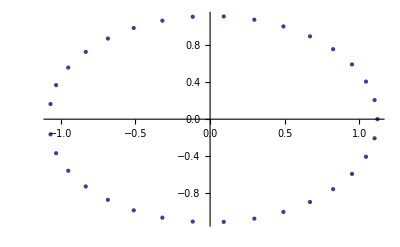

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,pzeros2[jj,10000000000]}]]
```

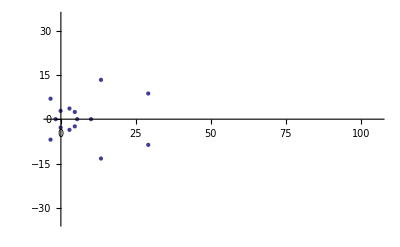

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,pzerosa[jj,1000000]}]]
```

```mathematica
Expand[pza[ff,10000,z]]
```

1+0.56733 z+1.81209 z^2-1.47941 z^3+1.18578 z^4-0.485266 z^5+0.140903 z^6-0.0263209 z^7+0.00346853 z^8-0.000311406 z^9+0.0000218201 z^10-1.13957×10^-6 z^11+4.07097×10^-8 z^12+1.6059×10^-10 z^13

```mathematica
Expand[pza[ff,100000,z]]
```

$Aborted

```mathematica
N[Expand[Sum[ bin[z,k]3^k,{k,0,3}]]]/.z->1
```

4.

```mathematica
pzerosa[jj,1000000]
```

{-3.45042-6.92631 ⅈ,-3.45042+6.92631 ⅈ,-1.75739,-0.0911848-2.80665 ⅈ,-0.0911848+2.80665 ⅈ,2.863-3.61048 ⅈ,2.863+3.61048 ⅈ,4.64524-2.43395 ⅈ,4.64524+2.43395 ⅈ,5.4378,10.0628,13.374-13.3145 ⅈ,13.374+13.3145 ⅈ,29.1437-8.68903 ⅈ,29.1437+8.68903 ⅈ,42.1878-52.3997 ⅈ,42.1878+52.3997 ⅈ,319.776-189.885 ⅈ,319.776+189.885 ⅈ}

```mathematica
pzeros[fo,10]
```

{-57.4386-0.665461 ⅈ,0.00504456-0.0000508451 ⅈ,0.766848-0.00115505 ⅈ}

```mathematica
Sum[fo[n],{n,1,20}]
```

67+ⅈ

```mathematica
Expand[pz[fo,10,z]]
```

1-(399/2+2 ⅈ) z+(255+3 ⅈ) z^2+(9 z^3)/2

```mathematica
Product[1-1/j,{j,pzeros[fo,10]}]
```

61.+1. ⅈ

```mathematica
Sum[ (z Log[Zeta[s]])^k/k! ,{k,0,Infinity}]
```

Zeta[s]^z

```mathematica
px[s_,z_,t_]:=Sum[ (z Log[(1-2^(1-s))Zeta[s]])^k/k! ,{k,0,t}]
pxzeros[s_,t_]:=List@@NRoots[px[s,z,t]==0,z][[All,2]]
```

```mathematica
1-1/pxzeros[2,20]//TableForm
```

1.01046-0.00893346 ⅈ
1.01046+0.00893346 ⅈ
1.00877-0.0148524 ⅈ
1.00877+0.0148524 ⅈ
1.00491-0.0195277 ⅈ
1.00491+0.0195277 ⅈ
0.999559-0.0226156 ⅈ
0.999559+0.0226156 ⅈ
0.993336-0.0238402 ⅈ
0.993336+0.0238402 ⅈ
0.986871-0.023075 ⅈ
0.986871+0.023075 ⅈ
0.980785-0.0203657 ⅈ
0.980785+0.0203657 ⅈ
0.97565-0.0159293 ⅈ
0.97565+0.0159293 ⅈ
0.971939-0.0101363 ⅈ
0.971939+0.0101363 ⅈ
0.969994-0.00347788 ⅈ
0.969994+0.00347788 ⅈ

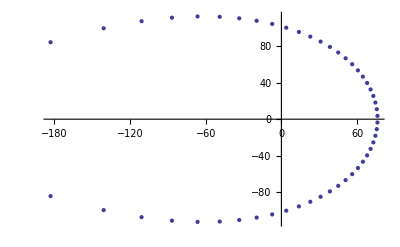

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,pxzeros[2,50]}]]
```

```mathematica
Product[ 1-1/j,{j,pxzeros[2,50]}]
```

0.822467+3.46945×10^-18 ⅈ

```mathematica
-Sum[1/j,{j,pxzeros[2,50]}]
```

-0.195446+0. ⅈ

```mathematica
N[Log[Pi^2/12]]
```

-0.195447

```mathematica
N[Pi^2/12]
```

0.822467

```mathematica
Expand[px[2,z,20]]
```

1+z Log[π^2/12]+1/2 z^2 Log[π^2/12]^2+1/6 z^3 Log[π^2/12]^3+1/24 z^4 Log[π^2/12]^4+1/120 z^5 Log[π^2/12]^5+1/720 z^6 Log[π^2/12]^6+(z^7 Log[π^2/12]^7)/5040+(z^8 Log[π^2/12]^8)/40320+(z^9 Log[π^2/12]^9)/362880+(z^10 Log[π^2/12]^10)/3628800+(z^11 Log[π^2/12]^11)/39916800+(z^12 Log[π^2/12]^12)/479001600+(z^13 Log[π^2/12]^13)/6227020800+(z^14 Log[π^2/12]^14)/87178291200+(z^15 Log[π^2/12]^15)/1307674368000+(z^16 Log[π^2/12]^16)/20922789888000+(z^17 Log[π^2/12]^17)/355687428096000+(z^18 Log[π^2/12]^18)/6402373705728000+(z^19 Log[π^2/12]^19)/121645100408832000+(z^20 Log[π^2/12]^20)/2432902008176640000

```mathematica
gx[s_,z_,t_]:=Sum[ (z Log[Zeta[s]])^k/k! ,{k,0,t}]
gxzeros[s_,t_]:=List@@NRoots[gx[s,z,t]==0,z][[All,2]]
```

```mathematica
N[gx[4,z,20]]
```

1.+0.0791099 z+0.00312919 z^2+0.0000825165 z^3+1.63197×10^-6 z^4+2.58209×10^-8 z^5+3.40449×10^-10 z^6+3.84755×10^-12 z^7+3.80474×10^-14 z^8+3.34436×10^-16 z^9+2.64572×10^-18 z^10+1.90275×10^-20 z^11+1.25439×10^-22 z^12+7.63341×10^-25 z^13+4.31342×10^-27 z^14+2.27489×10^-29 z^15+1.12479×10^-31 z^16+5.23423×10^-34 z^17+2.30044×10^-36 z^18+9.5783×10^-39 z^19+3.78869×10^-41 z^20

```mathematica
gxzeros[4,20]
```

{-81.2453-9.41692 ⅈ,-81.2453+9.41692 ⅈ,-77.8803-28.1321 ⅈ,-77.8803+28.1321 ⅈ,-71.0529-46.4806 ⅈ,-71.0529+46.4806 ⅈ,-60.5528-64.1806 ⅈ,-60.5528+64.1806 ⅈ,-46.0198-80.8834 ⅈ,-46.0198+80.8834 ⅈ,-26.8683-96.1202 ⅈ,-26.8683+96.1202 ⅈ,-2.12877-109.201 ⅈ,-2.12877+109.201 ⅈ,29.9239-118.991 ⅈ,29.9239+118.991 ⅈ,72.8409-123.316 ⅈ,72.8409+123.316 ⅈ,136.577-116.663 ⅈ,136.577+116.663 ⅈ}

```mathematica
Product[ 1-1/j,{j, gxzeros[2,30]}]
```

1.64493-1.38778×10^-17 ⅈ

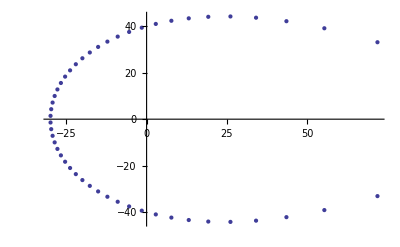

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,gxzeros[2,50]}]]
```

```mathematica
gam[t_] := E^(-EulerGamma t) / t Product[ (1+t/n)^-1 E^(t/n),{n,1,Infinity}]
lgam[t_] := Log[E^(-EulerGamma t) / t Product[ (1+t/n)^-1 E^(t/n),{n,1,Infinity}]]
lgam2[t_] := (-EulerGamma t) -Log[t]+Log[ Product[ (1+t/n)^-1 E^(t/n),{n,1,Infinity}]]
lgam3[t_] := (-EulerGamma t) -Log[t]+Sum[Log[ (1+t/n)^-1 E^(t/n)],{n,1,Infinity}]
lgam4[t_] := (-EulerGamma t) -Log[t]+Sum[-Log[ (1+t/n)]+t/n,{n,1,Infinity}]
```

```mathematica
N[lgam4[6.2+I]]
```

5.04524+1.74679 ⅈ

```mathematica
Log[Gamma[6.2+I]]
```

5.04524+1.74679 ⅈ

```mathematica
D[Expand[pza[fe,10,z]],z]/.z->0
```

5.33333

```mathematica
D[Expand[pza[ff,10,z]],z]/.z->0
```

0.718282

```mathematica
Table[{n,D[pz[fr,n,z],z]/.z->0},{n,1,10}]//TableForm
```

1 | 0
2 | fs[1]
3 | fs[1]+fs[2]
4 | fs[1]-fs[1]^2/2+fs[2]+fs[3]
5 | fs[1]-fs[1]^2/2+fs[2]+fs[3]+fs[4]
6 | fs[1]+fs[2]+1/2 (-fs[1] fs[2]-fs[1] (fs[1]+fs[2]))+fs[3]+fs[4]+fs[5]
7 | fs[1]+fs[2]+1/2 (-fs[1] fs[2]-fs[1] (fs[1]+fs[2]))+fs[3]+fs[4]+fs[5]+fs[6]
8 | fs[1]+fs[1]^3/3+fs[2]+fs[3]+1/2 (-fs[1] fs[2]-fs[1] fs[3]-fs[1] (fs[1]+fs[2]+fs[3]))+fs[4]+fs[5]+fs[6]+fs[7]
9 | fs[1]+fs[1]^3/3+fs[2]+fs[3]+1/2 (-fs[2] (fs[1]+fs[2])-fs[1] fs[3]-fs[1] (fs[1]+fs[2]+fs[3]))+fs[4]+fs[5]+fs[6]+fs[7]+fs[8]
10 | fs[1]+fs[1]^3/3+fs[2]+fs[3]+fs[4]+1/2 (-fs[2] (fs[1]+fs[2])-fs[1] fs[3]-fs[1] fs[4]-fs[1] (fs[1]+fs[2]+fs[3]+fs[4]))+fs[5]+fs[6]+fs[7]+fs[8]+fs[9]

```mathematica
oo[n_, k_] := Sum[ 1/((j-1)!)(1/k-oo[n/j,k+1]),{j,2,n}]
```

```mathematica
N[oo[10,1]]
```

0.718282

```mathematica
pza[ff,100000,10]
```

22025.1

```mathematica
N[E^10]
```

22026.5

```mathematica
N[1/10000!]
```

3.51338286771432×10^-35660

```mathematica
Sum[ (-1)^(k+1)/k (E-1)^k,{k,1,Infinity}]
```

Sum::div: Sum does not converge.

∑_(k=1)^∞ ((-1)^(1+k) (-1+ⅇ)^k)/k

```mathematica
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
e2[n_, k_] := e2[n,k]=Sum[ 1/((j-1)!) e2[Floor[n/j], k-1],{j,2,n}]
e2[n_, 0] := UnitStep[n-1]
ez[n_, z_] := Sum[ bin[ z,k]e2[n,k],{k,0,Log[2,n]}]
dez[n_, z_] := ez[n,z]-ez[n-1,z]
ldez[n_, k_] := D[dez[n,z],{z,k}]/.z->0
ezl[n_, k_] := ezl[n,k]=D[ez[n,z],{z,k}]/.z->0
ezlz[n_, z_] := Sum[ z^k / (k!) ezl[n,k],{k,0,Log[2,n]}]
cosz[n_, z_] := cosz[n,z]=Sum[ (D[Cos[x],{x,k}]/.x->0)z^k/ (k!) ezl[n,k],{k,0,Log[2,n]}]
sinz[n_, z_] := sinz[n,z]=Sum[ (D[Sin[x],{x,k}]/.x->0)z^k/ (k!) ezl[n,k],{k,0,Log[2,n]}]
dcosz[n_,z_] := cosz[n,z]-cosz[n-1,z]
dsinz[n_,z_] := sinz[n,z]-sinz[n-1,z]
```

```mathematica
Grid[Table[((D[Expand[ez[n,z]-ez[n-1,z]],{z,k}]/.z->0)),{k,1,4},{n,2,20}]]
```

1 | 1/2 | -1/3 | 1/24 | -59/120 | 1/720 | 841/5040 | -5039/40320 | -15119/362880 | 1/3628800 | 16299361/39916800 | 1/479001600 | -8648639/6227020800 | -1816214399/87178291200 | -127394467199/1307674368000 | 1/20922789888000 | 87431004460801/355687428096000 | 1/6402373705728000 | 4223452987353601/121645100408832000
0 | 0 | 1 | 0 | 1 | 0 | -2/3 | 1/4 | 1/12 | 0 | -79/60 | 0 | 1/360 | 1/24 | 1121/2520 | 0 | -14951/20160 | 0 | -20159/181440
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | -1 | 0 | 3/4 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0

```mathematica
N[Sum[ dez[j,2] ez[240/j,3+I],{j,1,240}]]
```

82.2577+124.894 ⅈ

```mathematica
N[ez[240,5+I]]
```

82.2577+124.894 ⅈ

```mathematica
Expand[pza[ff,40000,z]]
```

1+0.634243 z+1.73374 z^2-1.6071 z^3+1.49646 z^4-0.755491 z^5+0.273172 z^6-0.0672299 z^7+0.0118127 z^8-0.0014458 z^9+0.00012414 z^10-7.33435×10^-6 z^11+3.22744×10^-7 z^12-1.13705×10^-8 z^13+2.99195×10^-10 z^14+7.64716×10^-13 z^15

```mathematica
pza[fh,4000,1]
```

0.540302+0.841471 ⅈ

```mathematica
N[E^(1I)]
```

0.540302+0.841471 ⅈ

```mathematica
pz2[ff,5,z]
```

1.+1. z+0.5 z^2+0.166667 z^3+0.0416667 z^4+0.00833333 z^5

```mathematica
N[pz2[ff,20,2]pz2[ff,20,3+I]]
```

80.188+124.885 ⅈ

```mathematica
N[pz2[ff,20,5+I]]
```

80.188+124.885 ⅈ

```mathematica
Expand[N[cosz[100,z]+I sinz[100,z]]]
```

1.+(0.+0.937597 ⅈ) z-0.627118 z^2-(0.+0.0689598 ⅈ) z^3+0.0894681 z^4-(0.+0.0104167 ⅈ) z^5-0.00555556 z^6

```mathematica
Expand[N[ez[100,z I]]]
```

1.+(0.+0.937597 ⅈ) z-(0.627118+0. ⅈ) z^2-(0.+0.0689598 ⅈ) z^3+(0.0894681+0. ⅈ) z^4-(0.+0.0104167 ⅈ) z^5-(0.00555556+0. ⅈ) z^6

```mathematica
N[cosz[1000,Pi/2]]
```

0.685114

```mathematica
N[sinz[1000,-Pi/2]]
```

-1.8145

```mathematica
N[sinz[100,2+3I]]
```

3.77651+8.4109 ⅈ

```mathematica
N[Sum[ dsinz[j,2]cosz[100/j,3I],{j,1,100}] + Sum[ dcosz[j,2]sinz[100/j,3I],{j,1,100}]]
```

3.77651+8.4109 ⅈ

```mathematica
N[cosz[100,2+3I]]
```

-17.8167-13.6616 ⅈ

```mathematica
N[Sum[ dcosz[j,2]cosz[100/j,3I],{j,1,100}] - Sum[ dsinz[j,2]sinz[100/j,3I],{j,1,100}]]
```

-17.8167-13.6616 ⅈ

```mathematica
N[sinz[100,2(2+3I)]]
```

-11.5391+199.66 ⅈ

```mathematica
2N[Sum[ dsinz[j,2+3I]cosz[100/j,2+3I],{j,1,100}]]
```

-11.5391+199.66 ⅈ

```mathematica
N[ cosz[100,2(2+3I)]]
```

-880.36+92.5196 ⅈ

```mathematica
N[Sum[ dcosz[j,2+3I]cosz[100/j,2+3I],{j,1,100}] - Sum[ dsinz[j,2+3I]sinz[100/j,2+3I],{j,1,100}]]
```

-880.36+92.5196 ⅈ

```mathematica
N[Sum[ dcosz[j,2+3I]cosz[100/j,2+3I],{j,1,100}] + Sum[ dsinz[j,2+3I]sinz[100/j,2+3I],{j,1,100}]]
```

1.

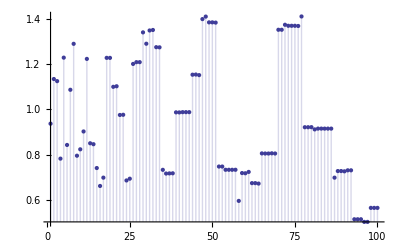

```mathematica
DiscretePlot[D[Expand[N[pza[ff,100n,z ]]],z]/.z->0,{n,1,100}]
```

```mathematica
N[Expand[ez[100,z]]]
```

1.+0.937597 z+0.627118 z^2+0.0689598 z^3+0.0894681 z^4-0.0104167 z^5+0.00555556 z^6

```mathematica
Expand[pza[ff,10000,z]]
```

1+0.56733 z+1.81209 z^2-1.47941 z^3+1.18578 z^4-0.485266 z^5+0.140903 z^6-0.0263209 z^7+0.00346853 z^8-0.000311406 z^9+0.0000218201 z^10-1.13957×10^-6 z^11+4.07097×10^-8 z^12+1.6059×10^-10 z^13

```mathematica
Grid[Table[ldez[n,k],{k,1,4},{n,2,20}]]
```

1 | 1/2 | -1/3 | 1/24 | -59/120 | 1/720 | 841/5040 | -5039/40320 | -15119/362880 | 1/3628800 | 16299361/39916800 | 1/479001600 | -8648639/6227020800 | -1816214399/87178291200 | -127394467199/1307674368000 | 1/20922789888000 | 87431004460801/355687428096000 | 1/6402373705728000 | 4223452987353601/121645100408832000
0 | 0 | 1 | 0 | 1 | 0 | -2/3 | 1/4 | 1/12 | 0 | -79/60 | 0 | 1/360 | 1/24 | 1121/2520 | 0 | -14951/20160 | 0 | -20159/181440
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3/2 | 0 | 0 | 0 | -1 | 0 | 3/4 | 0 | 1/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0

```mathematica
Table[ldez[2^n,1],{n,1,5}]
```

{1,-1/3,841/5040,-127394467199/1307674368000,503866402976241324312641187840001/8222838654177922817725562880000000}

```mathematica
DiscretePlot[ D[ez[n,z],z]/.z->0,{n,2,100}]
```

```mathematica
Sum[1/(x+1)^k/k,{k,1,Infinity}]
```

-Log[x/(1+x)]

```mathematica
Sum[-(1-x)^k/k,{k,1,Infinity}]
```

Log[x]

```mathematica
Sum[-(1-x)^k/k,{k,1,Infinity}]
```

```mathematica
Sum[(-1)^(k+1) x^k/k,{k,1,Infinity}]
```

Log[1+x]

```mathematica
Sum[(-1)^(k+1) (x-1)^k/k,{k,1,Infinity}]
```

Log[x]

```mathematica
Sum[ z^k Log[x]^k/k!,{k,0,Infinity}]
```

x^z

```mathematica
lx[n_, x_, k_] := lx[n,x,k]=Sum[ (-j^-1)(1-x)^j lx[Floor[n/j],x,k-1],{j,1,n}]
lx[n_,x_,0]:=UnitStep[n-1]
xz[n_, x_, z_] := Sum[   z^k/(k!) lx[n,x,k],{k,0,70}]
```

```mathematica
lx[3000,1.5,16]
```

4.61208×10^-7

```mathematica
N[Log[1.5]]^16
```

5.33649×10^-7

```mathematica
Expand[xz[500,N[1/E],z]]/.z->-1
```

2.71826

```mathematica
1/(N[1/E]^2)
```

7.38906

```mathematica
N[ezl[500,2]]
```

-0.238567

```mathematica
lx[500,N[1/E],2]
```

1.

```mathematica
Log[(a-1)!]+Log[(b-1)!]
```

```mathematica
-Log[(-1+a)!]-Log[(-1+b)!]
```

-Log[(-1+a)!]-Log[(-1+b)!]

```mathematica
Expand[pza[ff,10000,z]]
```

1+0.56733 z+1.81209 z^2-1.47941 z^3+1.18578 z^4-0.485266 z^5+0.140903 z^6-0.0263209 z^7+0.00346853 z^8-0.000311406 z^9+0.0000218201 z^10-1.13957×10^-6 z^11+4.07097×10^-8 z^12+1.6059×10^-10 z^13

```mathematica
Grid[Table[pza[ff,10000,a+ b I],{a,-3,3,.6},{b,-3,3,.6}]]
```

-118.184-120.835 ⅈ | -125.12-12.8964 ⅈ | -77.7681+58.4357 ⅈ | -10.1428+78.8621 ⅈ | 45.6188+52.9852 ⅈ | 66.9091+0. ⅈ | 45.6188-52.9852 ⅈ | -10.1428-78.8621 ⅈ | -77.7681-58.4357 ⅈ | -125.12+12.8964 ⅈ | -118.184+120.835 ⅈ
-36.2469-77.5718 ⅈ | -55.0939-24.0024 ⅈ | -40.465+16.2636 ⅈ | -10.549+31.9049 ⅈ | 16.3285+23.2845 ⅈ | 26.8939+0. ⅈ | 16.3285-23.2845 ⅈ | -10.549-31.9049 ⅈ | -40.465-16.2636 ⅈ | -55.0939+24.0024 ⅈ | -36.2469+77.5718 ⅈ
-1.72548-42.4949 ⅈ | -19.6081-19.7664 ⅈ | -18.4404+0.730831 ⅈ | -7.02362+10.7969 ⅈ | 4.82234+9.11778 ⅈ | 9.68309+0. ⅈ | 4.82234-9.11778 ⅈ | -7.02362-10.7969 ⅈ | -18.4404-0.730831 ⅈ | -19.6081+19.7664 ⅈ | -1.72548+42.4949 ⅈ
8.48289-19.1168 ⅈ | -4.0194-12.1651 ⅈ | -6.81631-3.1756 ⅈ | -3.49348+2.40558 ⅈ | 1.12322+2.92987 ⅈ | 3.15113+0. ⅈ | 1.12322-2.92987 ⅈ | -3.49348-2.40558 ⅈ | -6.81631+3.1756 ⅈ | -4.0194+12.1651 ⅈ | 8.48289+19.1168 ⅈ
8.11545-6.1614 ⅈ | 1.23447-6.03318 ⅈ | -1.50901-3.00789 ⅈ | -1.07952-0.362778 ⅈ | 0.442785+0.517466 ⅈ | 1.19363+0. ⅈ | 0.442785-0.517466 ⅈ | -1.07952+0.362778 ⅈ | -1.50901+3.00789 ⅈ | 1.23447+6.03318 ⅈ | 8.11545+6.1614 ⅈ
4.57207-0.653437 ⅈ | 1.91479-2.56437 ⅈ | 0.443461-2.12244 ⅈ | 0.289598-1.05779 ⅈ | 0.739846-0.316688 ⅈ | 1.+0. ⅈ | 0.739846+0.316688 ⅈ | 0.289598+1.05779 ⅈ | 0.443461+2.12244 ⅈ | 1.91479+2.56437 ⅈ | 4.57207+0.653437 ⅈ
1.22423+0.417724 ⅈ | 1.13168-1.3962 ⅈ | 0.938413-1.7147 ⅈ | 1.04758-1.27747 ⅈ | 1.31444-0.63304 ⅈ | 1.44811+0. ⅈ | 1.31444+0.63304 ⅈ | 1.04758+1.27747 ⅈ | 0.938413+1.7147 ⅈ | 1.13168+1.3962 ⅈ | 1.22423-0.417724 ⅈ
-0.899336-0.654071 ⅈ | 0.292279-1.7566 ⅈ | 1.03856-2.02204 ⅈ | 1.62654-1.64254 ⅈ | 2.05396-0.895945 ⅈ | 2.21479+0. ⅈ | 2.05396+0.895945 ⅈ | 1.62654+1.64254 ⅈ | 1.03856+2.02204 ⅈ | 0.292279+1.7566 ⅈ | -0.899336+0.654071 ⅈ
-1.94896-2.49749 ⅈ | -0.174666-3.01609 ⅈ | 1.24698-2.98373 ⅈ | 2.34978-2.3607 ⅈ | 3.07146-1.29459 ⅈ | 3.32497+0. ⅈ | 3.07146+1.29459 ⅈ | 2.34978+2.3607 ⅈ | 1.24698+2.98373 ⅈ | -0.174666+3.01609 ⅈ | -1.94896+2.49749 ⅈ
-2.51249-4.57538 ⅈ | -0.309393-4.88849 ⅈ | 1.75635-4.56512 ⅈ | 3.45009-3.53114 ⅈ | 4.56651-1.92289 ⅈ | 4.95694+0. ⅈ | 4.56651+1.92289 ⅈ | 3.45009+3.53114 ⅈ | 1.75635+4.56512 ⅈ | -0.309393+4.88849 ⅈ | -2.51249+4.57538 ⅈ
-3.20313-6.97438 ⅈ | -0.300157-7.44897 ⅈ | 2.64111-6.89184 ⅈ | 5.13698-5.29581 ⅈ | 6.80385-2.87456 ⅈ | 7.38906+0. ⅈ | 6.80385+2.87456 ⅈ | 5.13698+5.29581 ⅈ | 2.64111+6.89184 ⅈ | -0.300157+7.44897 ⅈ | -3.20313+6.97438 ⅈ

```mathematica
Grid[Table[E^(a+ b I),{a,-2,2,.4},{b,-2,2,.4}]]
```

-0.0563193-0.12306 ⅈ | -0.00395173-0.135278 ⅈ | 0.0490398-0.126138 ⅈ | 0.094289-0.0970836 ⅈ | 0.124652-0.052702 ⅈ | 0.135335+0. ⅈ | 0.124652+0.052702 ⅈ | 0.094289+0.0970836 ⅈ | 0.0490398+0.126138 ⅈ | -0.00395173+0.135278 ⅈ | -0.0563193+0.12306 ⅈ
-0.0840186-0.183584 ⅈ | -0.00589528-0.20181 ⅈ | 0.0731588-0.188175 ⅈ | 0.140663-0.144832 ⅈ | 0.185959-0.0786222 ⅈ | 0.201897+0. ⅈ | 0.185959+0.0786222 ⅈ | 0.140663+0.144832 ⅈ | 0.0731588+0.188175 ⅈ | -0.00589528+0.20181 ⅈ | -0.0840186+0.183584 ⅈ
-0.125341-0.273875 ⅈ | -0.00879473-0.301066 ⅈ | 0.10914-0.280725 ⅈ | 0.209844-0.216064 ⅈ | 0.277418-0.117291 ⅈ | 0.301194+0. ⅈ | 0.277418+0.117291 ⅈ | 0.209844+0.216064 ⅈ | 0.10914+0.280725 ⅈ | -0.00879473+0.301066 ⅈ | -0.125341+0.273875 ⅈ
-0.186987-0.408574 ⅈ | -0.0131202-0.449137 ⅈ | 0.162818-0.418792 ⅈ | 0.313051-0.322329 ⅈ | 0.413859-0.174977 ⅈ | 0.449329+0. ⅈ | 0.413859+0.174977 ⅈ | 0.313051+0.322329 ⅈ | 0.162818+0.418792 ⅈ | -0.0131202+0.449137 ⅈ | -0.186987+0.408574 ⅈ
-0.278952-0.60952 ⅈ | -0.019573-0.670034 ⅈ | 0.242896-0.624764 ⅈ | 0.467016-0.480858 ⅈ | 0.617406-0.261035 ⅈ | 0.67032+0. ⅈ | 0.617406+0.261035 ⅈ | 0.467016+0.480858 ⅈ | 0.242896+0.624764 ⅈ | -0.019573+0.670034 ⅈ | -0.278952+0.60952 ⅈ
-0.416147-0.909297 ⅈ | -0.0291995-0.999574 ⅈ | 0.362358-0.932039 ⅈ | 0.696707-0.717356 ⅈ | 0.921061-0.389418 ⅈ | 1. | 0.921061+0.389418 ⅈ | 0.696707+0.717356 ⅈ | 0.362358+0.932039 ⅈ | -0.0291995+0.999574 ⅈ | -0.416147+0.909297 ⅈ
-0.620818-1.35651 ⅈ | -0.0435606-1.49119 ⅈ | 0.540574-1.39044 ⅈ | 1.03936-1.07017 ⅈ | 1.37406-0.580944 ⅈ | 1.49182+0. ⅈ | 1.37406+0.580944 ⅈ | 1.03936+1.07017 ⅈ | 0.540574+1.39044 ⅈ | -0.0435606+1.49119 ⅈ | -0.620818+1.35651 ⅈ
-0.926152-2.02368 ⅈ | -0.0649847-2.22459 ⅈ | 0.806442-2.07429 ⅈ | 1.55055-1.59651 ⅈ | 2.04986-0.866666 ⅈ | 2.22554+0. ⅈ | 2.04986+0.866666 ⅈ | 1.55055+1.59651 ⅈ | 0.806442+2.07429 ⅈ | -0.0649847+2.22459 ⅈ | -0.926152+2.02368 ⅈ
-1.38166-3.01897 ⅈ | -0.0969458-3.3187 ⅈ | 1.20307-3.09448 ⅈ | 2.31315-2.38171 ⅈ | 3.05803-1.29291 ⅈ | 3.32012+0. ⅈ | 3.05803+1.29291 ⅈ | 2.31315+2.38171 ⅈ | 1.20307+3.09448 ⅈ | -0.0969458+3.3187 ⅈ | -1.38166+3.01897 ⅈ
-2.06119-4.50378 ⅈ | -0.144626-4.95092 ⅈ | 1.79477-4.61642 ⅈ | 3.45081-3.55309 ⅈ | 4.56204-1.9288 ⅈ | 4.95303+0. ⅈ | 4.56204+1.9288 ⅈ | 3.45081+3.55309 ⅈ | 1.79477+4.61642 ⅈ | -0.144626+4.95092 ⅈ | -2.06119+4.50378 ⅈ
-3.07493-6.71885 ⅈ | -0.215757-7.38591 ⅈ | 2.67748-6.88689 ⅈ | 5.148-5.30058 ⅈ | 6.80577-2.87743 ⅈ | 7.38906+0. ⅈ | 6.80577+2.87743 ⅈ | 5.148+5.30058 ⅈ | 2.67748+6.88689 ⅈ | -0.215757+7.38591 ⅈ | -3.07493+6.71885 ⅈ

```mathematica
Grid[Table[pza[ff,10000,a+ b I]-E^(a + b I ),{a,-3,3,.6},{b,-3,3,.6}]]
```

-21.5457-1497.35 ⅈ | -761.331-693.846 ⅈ | -735.824+109.399 ⅈ | -261.17+512.894 ⅈ | 248.371+419.476 ⅈ | 460.149+0. ⅈ | 248.371-419.476 ⅈ | -261.17-512.894 ⅈ | -735.824-109.399 ⅈ | -761.331+693.846 ⅈ | -21.5457+1497.35 ⅈ
271.723-616.989 ⅈ | -182.945-387.928 ⅈ | -281.123-52.3715 ⅈ | -135.014+154.842 ⅈ | 64.4098+151.539 ⅈ | 152.215+0. ⅈ | 64.4098-151.539 ⅈ | -135.014-154.842 ⅈ | -281.123+52.3715 ⅈ | -182.945+387.928 ⅈ | 271.723+616.989 ⅈ
236.752-177.301 ⅈ | 7.09808-170.486 ⅈ | -83.7396-58.5093 ⅈ | -56.9525+32.8213 ⅈ | 10.2796+46.9511 ⅈ | 42.7863+0. ⅈ | 10.2796-46.9511 ⅈ | -56.9525-32.8213 ⅈ | -83.7396+58.5093 ⅈ | 7.09808+170.486 ⅈ | 236.752+177.301 ⅈ
127.856-3.72618 ⅈ | 39.1537-52.5812 ⅈ | -13.3805-31.3415 ⅈ | -18.5496+1.01156 ⅈ | -0.84982+11.4336 ⅈ | 9.38189+0. ⅈ | -0.84982-11.4336 ⅈ | -18.5496-1.01156 ⅈ | -13.3805+31.3415 ⅈ | 39.1537+52.5812 ⅈ | 127.856+3.72618 ⅈ
42.494+35.7435 ⅈ | 24.4338-4.75189 ⅈ | 3.53499-10.3186 ⅈ | -3.78393-2.81013 ⅈ | -1.19123+1.70393 ⅈ | 1.28148+0. ⅈ | -1.19123-1.70393 ⅈ | -3.78393+2.81013 ⅈ | 3.53499+10.3186 ⅈ | 24.4338+4.75189 ⅈ | 42.494-35.7435 ⅈ
0.501234+24.778 ⅈ | 7.3952+6.23565 ⅈ | 3.38592-1.05624 ⅈ | 0.0811037-1.1904 ⅈ | -0.330528-0.0583084 ⅈ | 0.+0. ⅈ | -0.330528+0.0583084 ⅈ | 0.0811037+1.1904 ⅈ | 3.38592+1.05624 ⅈ | 7.3952-6.23565 ⅈ | 0.501234-24.778 ⅈ
-9.50595+6.75516 ⅈ | -0.687161+3.93457 ⅈ | 0.843727+0.920956 ⅈ | 0.336175-0.0825363 ⅈ | 0.00686235-0.0813466 ⅈ | -0.0270856+0. ⅈ | 0.00686235+0.0813466 ⅈ | 0.336175+0.0825363 ⅈ | 0.843727-0.920956 ⅈ | -0.687161-3.93457 ⅈ | -9.50595-6.75516 ⅈ
-5.27274-2.67332 ⅈ | -1.7586+0.394219 ⅈ | -0.256666+0.422273 ⅈ | 0.0439096+0.110746 ⅈ | 0.0238952+0.00438912 ⅈ | 0.00485502+0. ⅈ | 0.0238952-0.00438912 ⅈ | 0.0439096-0.110746 ⅈ | -0.256666-0.422273 ⅈ | -1.7586-0.394219 ⅈ | -5.27274+2.67332 ⅈ
0.288606-3.26822 ⅈ | -0.43186-0.793026 ⅈ | -0.205613-0.0834832 ⅈ | -0.0443002+0.0188182 ⅈ | -0.00245115+0.00871033 ⅈ | 0.00175243+0. ⅈ | -0.00245115-0.00871033 ⅈ | -0.0443002-0.0188182 ⅈ | -0.205613+0.0834832 ⅈ | -0.43186+0.793026 ⅈ | 0.288606+3.26822 ⅈ
1.97668-0.403477 ⅈ | 0.395198-0.31694 ⅈ | 0.0363911-0.10687 ⅈ | -0.007313-0.0210753 ⅈ | -0.0035108-0.00192363 ⅈ | -0.00118997+0. ⅈ | -0.0035108+0.00192363 ⅈ | -0.007313+0.0210753 ⅈ | 0.0363911+0.10687 ⅈ | 0.395198+0.31694 ⅈ | 1.97668+0.403477 ⅈ
0.55134+1.27522 ⅈ | 0.220867+0.232239 ⅈ | 0.0605337+0.0233881 ⅈ | 0.0114039-0.00204373 ⅈ | 0.00123102-0.00135544 ⅈ | 0.+0. ⅈ | 0.00123102+0.00135544 ⅈ | 0.0114039+0.00204373 ⅈ | 0.0605337-0.0233881 ⅈ | 0.220867-0.232239 ⅈ | 0.55134-1.27522 ⅈ

```mathematica
Grid[Table[pza[ff,100000,a+ b I]-E^(a + b I ),{a,-3,3,.6},{b,-3,3,.6}]]
```

1738.61+64.7318 ⅈ | 538.047-824.394 ⅈ | -309.506-492.703 ⅈ | -358.541+93.1447 ⅈ | 21.0568+267.194 ⅈ | 237.317+0. ⅈ | 21.0568-267.194 ⅈ | -358.541-93.1447 ⅈ | -309.506+492.703 ⅈ | 538.047+824.394 ⅈ | 1738.61-64.7318 ⅈ
506.075+401.926 ⅈ | 303.968-122.466 ⅈ | 0.649141-169.779 ⅈ | -89.7696-20.5304 ⅈ | -12.5227+54.3837 ⅈ | 44.8822+0. ⅈ | -12.5227-54.3837 ⅈ | -89.7696+20.5304 ⅈ | 0.649141+169.779 ⅈ | 303.968+122.466 ⅈ | 506.075-401.926 ⅈ
37.9632+234.939 ⅈ | 100.306+37.1114 ⅈ | 31.7413-35.422 ⅈ | -12.6012-16.645 ⅈ | -6.50429+6.16533 ⅈ | 4.92646+0. ⅈ | -6.50429-6.16533 ⅈ | -12.6012+16.645 ⅈ | 31.7413+35.422 ⅈ | 100.306-37.1114 ⅈ | 37.9632-234.939 ⅈ
-56.3934+68.3761 ⅈ | 11.8716+33.2004 ⅈ | 13.4481+0.849633 ⅈ | 1.49004-4.61276 ⅈ | -1.38297-0.605015 ⅈ | -0.254704+0. ⅈ | -1.38297+0.605015 ⅈ | 1.49004+4.61276 ⅈ | 13.4481-0.849633 ⅈ | 11.8716-33.2004 ⅈ | -56.3934-68.3761 ⅈ
-33.9542-2.6219 ⅈ | -7.40591+9.54604 ⅈ | 1.73994+3.63818 ⅈ | 1.23971-0.146436 ⅈ | 0.0197328-0.367843 ⅈ | -0.17489+0. ⅈ | 0.0197328+0.367843 ⅈ | 1.23971+0.146436 ⅈ | 1.73994-3.63818 ⅈ | -7.40591-9.54604 ⅈ | -33.9542+2.6219 ⅈ
-5.78418-12.4536 ⅈ | -4.30054-0.915183 ⅈ | -0.890751+0.951901 ⅈ | 0.13445+0.323351 ⅈ | 0.0797037-0.00925588 ⅈ | 0.+0. ⅈ | 0.0797037+0.00925588 ⅈ | 0.13445-0.323351 ⅈ | -0.890751-0.951901 ⅈ | -4.30054+0.915183 ⅈ | -5.78418+12.4536 ⅈ
3.85278-4.44913 ⅈ | -0.239241-1.70964 ⅈ | -0.408213-0.220944 ⅈ | -0.0964752+0.056406 ⅈ | 0.00204784+0.023542 ⅈ | 0.00751132+0. ⅈ | 0.00204784-0.023542 ⅈ | -0.0964752-0.056406 ⅈ | -0.408213+0.220944 ⅈ | -0.239241+1.70964 ⅈ | 3.85278+4.44913 ⅈ
2.52351+0.972416 ⅈ | 0.678858-0.2909 ⅈ | 0.0596424-0.174347 ⅈ | -0.0221573-0.0346435 ⅈ | -0.00793265-0.00054708 ⅈ | -0.00155843+0. ⅈ | -0.00793265+0.00054708 ⅈ | -0.0221573+0.0346435 ⅈ | 0.0596424+0.174347 ⅈ | 0.678858+0.2909 ⅈ | 2.52351-0.972416 ⅈ
-0.112804+1.33269 ⅈ | 0.197032+0.283924 ⅈ | 0.0796028+0.0183708 ⅈ | 0.0147689-0.00911813 ⅈ | 0.000587594-0.00318053 ⅈ | -0.000624981+0. ⅈ | 0.000587594+0.00318053 ⅈ | 0.0147689+0.00911813 ⅈ | 0.0796028-0.0183708 ⅈ | 0.197032-0.283924 ⅈ | -0.112804-1.33269 ⅈ
-0.703708+0.106475 ⅈ | -0.127822+0.121987 ⅈ | -0.00668977+0.0397296 ⅈ | 0.00398417+0.00728907 ⅈ | 0.00143266+0.000600265 ⅈ | 0.000469755+0. ⅈ | 0.00143266-0.000600265 ⅈ | 0.00398417-0.00728907 ⅈ | -0.00668977-0.0397296 ⅈ | -0.127822-0.121987 ⅈ | -0.703708-0.106475 ⅈ
-0.139118-0.381321 ⅈ | -0.0762619-0.0620886 ⅈ | -0.0217953-0.00290354 ⅈ | -0.00405502+0.00185249 ⅈ | -0.000429422+0.000664949 ⅈ | 0.+0. ⅈ | -0.000429422-0.000664949 ⅈ | -0.00405502-0.00185249 ⅈ | -0.0217953+0.00290354 ⅈ | -0.0762619+0.0620886 ⅈ | -0.139118+0.381321 ⅈ

```mathematica
Grid[Table[pza[ff,100000,a+ b I]-E^(a + b I ),{a,-5,5,1},{b,-5,5,1}]]
```

64281.9+127047. ⅈ | 70012.-8226.66 ⅈ | 3673.47-37453.5 ⅈ | -22236.2-3892.39 ⅈ | -2000.46+15909. ⅈ | 14197.5 | -2000.46-15909. ⅈ | -22236.2+3892.39 ⅈ | 3673.47+37453.5 ⅈ | 70012.+8226.66 ⅈ | 64281.9-127047. ⅈ
-14225.7+41643.5 ⅈ | 15203.3+11057.5 ⅈ | 5842.11-6220.47 ⅈ | -3358.73-2736.16 ⅈ | -1073.78+2446.19 ⅈ | 2229.55 | -1073.78-2446.19 ⅈ | -3358.73+2736.16 ⅈ | 5842.11+6220.47 ⅈ | 15203.3-11057.5 ⅈ | -14225.7-41643.5 ⅈ
-12667.4+3816.66 ⅈ | 103.254+4731.59 ⅈ | 1738.61+64.7318 ⅈ | -115.217-679.215 ⅈ | -248.82+211.766 ⅈ | 237.317 | -248.82-211.766 ⅈ | -115.217+679.215 ⅈ | 1738.61-64.7318 ⅈ | 103.254-4731.59 ⅈ | -12667.4-3816.66 ⅈ
-2685.24-2929.32 ⅈ | -1040.63+519.582 ⅈ | 135.005+303.256 ⅈ | 72.4984-59.3562 ⅈ | -26.6498-3.9075 ⅈ | 11.3975 | -26.6498+3.9075 ⅈ | 72.4984+59.3562 ⅈ | 135.005-303.256 ⅈ | -1040.63-519.582 ⅈ | -2685.24+2929.32 ⅈ
660.709-1043.56 ⅈ | -183.135-229.268 ⅈ | -53.8889+34.8073 ⅈ | 8.79261+9.02696 ⅈ | 0.442975-2.04301 ⅈ | -0.348358 | 0.442975+2.04301 ⅈ | 8.79261-9.02696 ⅈ | -53.8889-34.8073 ⅈ | -183.135+229.268 ⅈ | 660.709+1043.56 ⅈ
364.891+192.253 ⅈ | 63.5883-49.0115 ⅈ | -5.78418-12.4536 ⅈ | -1.76572+0.882825 ⅈ | 0.158557+0.151955 ⅈ | 0. | 0.158557-0.151955 ⅈ | -1.76572-0.882825 ⅈ | -5.78418+12.4536 ⅈ | 63.5883+49.0115 ⅈ | 364.891-192.253 ⅈ
-83.6897+127.935 ⅈ | 10.4709+22.6089 ⅈ | 3.47243-0.167265 ⅈ | 0.0594098-0.390343 ⅈ | -0.0330419-0.00515427 ⅈ | 4.44089×10^-16 | -0.0330419+0.00515427 ⅈ | 0.0594098+0.390343 ⅈ | 3.47243+0.167265 ⅈ | 10.4709-22.6089 ⅈ | -83.6897-127.935 ⅈ
-43.349-47.5225 ⅈ | -8.98919+0.346529 ⅈ | -0.538972+0.930314 ⅈ | 0.059594+0.0861939 ⅈ | 0.00746396-0.00205494 ⅈ | 0. | 0.00746396+0.00205494 ⅈ | 0.059594-0.0861939 ⅈ | -0.538972-0.930314 ⅈ | -8.98919-0.346529 ⅈ | -43.349+47.5225 ⅈ
29.2173-10.3933 ⅈ | 1.79776-3.32544 ⅈ | -0.139118-0.381321 ⅈ | -0.034766-0.0114166 ⅈ | -0.00208239+0.00147848 ⅈ | 0. | -0.00208239-0.00147848 ⅈ | -0.034766+0.0114166 ⅈ | -0.139118+0.381321 ⅈ | 1.79776+3.32544 ⅈ | 29.2173+10.3933 ⅈ
-3.5957+16.7029 ⅈ | 0.733646+1.6229 ⅈ | 0.167374+0.0701458 ⅈ | 0.0158-0.00493253 ⅈ | 0.000679721-0.000940981 ⅈ | 0. | 0.000679721+0.000940981 ⅈ | 0.0158+0.00493253 ⅈ | 0.167374-0.0701458 ⅈ | 0.733646-1.6229 ⅈ | -3.5957-16.7029 ⅈ
-5.88107-9.16963 ⅈ | -0.754944-0.290649 ⅈ | -0.0784859+0.0453717 ⅈ | -0.00552141+0.00823736 ⅈ | -0.00020667+0.000701551 ⅈ | -2.84217×10^-14 | -0.00020667-0.000701551 ⅈ | -0.00552141-0.00823736 ⅈ | -0.0784859-0.0453717 ⅈ | -0.754944+0.290649 ⅈ | -5.88107+9.16963 ⅈ

```mathematica
Limit[(pza[ff,100000,z]-1)/z,z->0]
```

1.0943

```mathematica
Table[ D[pza[ff,1000n ,z],{z,1}]/.z->0,{n,1,35}]
```

{0.824825,1.09966,1.28911,0.987097,1.38306,0.71955,1.3505,0.922266,0.728064,0.56733,1.33983,1.23492,1.06204,0.531632,0.52117,1.17214,1.18722,1.36354,1.54283,1.43169,0.587194,0.554,0.554792,0.84169,0.823726,1.11178,1.09761,1.60824,1.64054,1.59375,1.62317,0.721691,0.693366,0.693199,0.585877}

```mathematica
zet2x[n_, s_, k_, x_] := Sum[ x^j j^-s zet2x[ Floor[n/j],s,k-1,x],{j,2,n}]
zet2x[n_, s_, 0, x_] := UnitStep[n-1]
zetzx[n_, s_, z_, x_] := Sum[ bin[ z,k] zet2x[n,s,k,x],{k,0,Log[2,n]}]
```

```mathematica
N[zetzx[300,0,3,1/3]]
```

1.58796

```mathematica
2. 13/12.
```

2.16667

```mathematica
2 7./6.
```

2.33333

```mathematica
Sum[ x^j,{j,2,Infinity}]
```

-x^2/(-1+x)

```mathematica
FullSimplify[1-x^2/(-1+x)]
```

1-x^2/(-1+x)

```mathematica
Sum[ x^j x^k,{j,2,Infinity},{k,2,Infinity}]
```

x^4/(-1+x)^2

```mathematica
Sum[ x^j x^k x^l,{j,2,Infinity},{k,2,Infinity}, {l,2,Infinity}]
```

-x^6/(-1+x)^3

```mathematica
ft[ t_] := (-1)^t x^(2t)/(x-1)^t
```

```mathematica
ft[0]
```

1

```mathematica
Sum[Binomial[z,n](-1)^n x^(2n)/(x-1)^n,{n,0,Infinity}]
```

((-1+x-x^2)/(-1+x))^z

```mathematica
Sum[(-1)^n x^(2n)/(x-1)^n,{n,0,3}]
```

1-x^2/(-1+x)+x^4/(-1+x)^2-x^6/(-1+x)^3

```mathematica
FullSimplify[(-1+x-x^2)/(-1+x)]
```

1/(1-x)-x

```mathematica
((-1+x-x^2)/(-1+x))^3
```

((-1+x-x^2)^3)/(-1+x)^3

```mathematica
N[(1/(1-x)-x)^3/.x->1/3]
```

1.58796

```mathematica
N[(1/(1-x)-(x-x^2)/(1-x))^3/.x->1/3]
```

1.58796

```mathematica
FullSimplify[(-1+x-x^2)/(-1+x)]
```

1/(1-x)-x

```mathematica
Sum[ (-1)^(j)x^j ,{j,2,Infinity}]
```

x^2/(1+x)

```mathematica
Sum[(-1)^(k+j) x^j x^k,{j,2,Infinity},{k,2,Infinity}]
```

x^4/(1+x)^2

```mathematica
Sum[ x^j,{j,2,Infinity}]
```

-x^2/(-1+x)

```mathematica
Sum[ x^j x^k,{j,2,Infinity},{k,2,Infinity}]
```

x^4/(-1+x)^2

```mathematica
Sum[Binomial[z,n] x^(2n)/(x+1)^n,{n,0,Infinity}]
```

((1+x+x^2)/(1+x))^z

```mathematica
Sum[Binomial[z,n](-1)^n x^(2n)/(x-1)^n,{n,0,Infinity}]
```

((-1+x-x^2)/(-1+x))^z

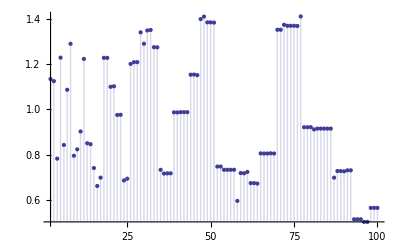

```mathematica
DiscretePlot[D[pza[ff,100n,  z],z]/.z->0,{n,2,100}]
```

```mathematica
Table[{n,D[pza[ff,n,  z]-pza[ff,n-1,  z],z]/.z->0},{n,2,100}]
```

{{2,1.},{3,0.5},{4,-0.333333},{5,0.0416667},{6,-0.491667},{7,0.00138889},{8,0.166865},{9,-0.124975},{10,-0.0416639},{11,2.75573×10^-7},{12,0.408333},{13,2.08768×10^-9},{14,-0.00138889},{15,-0.0208333},{16,-0.0974206},{17,4.77396×10^-14},{18,0.245809},{19,2.22045×10^-16},{20,0.0347195},{21,-0.000694444},{22,-2.75573×10^-7},{23,0},{24,-0.326488},{25,-0.000868056},{26,-2.08768×10^-9},{27,0.0416543},{28,0.00115741},{29,0},{30,0.0413181},{31,0},{32,0.0612765},{33,-1.37787×10^-7},{34,-4.77396×10^-14},{35,-0.0000578704},{36,-0.325014},{37,0},{38,0},{39,-1.04384×10^-9},{40,-0.0277837},{41,0},{42,0.00137731},{43,0},{44,2.29644×10^-7},{45,0.0104156},{46,0},{47,0},{48,0.25853},{49,-9.64506×10^-7},{50,0.001736},{51,-2.37588×10^-14},{52,1.73973×10^-9},{53,0},{54,-0.122892},{55,-1.14822×10^-8},{56,-0.000926201},{57,0},{58,0},{59,0},{60,-0.0548584},{61,0},{62,0},{63,0.000347188},{64,-0.0402558},{65,-8.69864×10^-11},{66,2.73277×10^-7},{67,0},{68,3.9746×10^-14},{69,0},{70,0.000115737},{71,0},{72,0.363991},{73,0},{74,0},{75,0.000868056},{76,0},{77,-3.82741×10^-10},{78,2.07028×10^-9},{79,0},{80,0.0220054},{81,-0.0156188},{82,0},{83,0},{84,-0.0018287},{85,-2.22045×10^-15},{86,0},{87,0},{88,-1.8377×10^-7},{89,0},{90,-0.0309},{91,-2.89968×10^-12},{92,0},{93,0},{94,0},{95,0},{96,-0.204196},{97,0},{98,1.92901×10^-6},{99,6.88865×10^-8},{100,-0.00231459}}

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dzeta[j_,s_,z_]:=j^-s Product[(-1)^p[[2]] bin[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[dzeta[j,s,z],{j,1,n}]
```

```mathematica
D[Expand[zeta[100,0,z]],z]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
Expand[Sum[ (D[dzeta[j,0,z],z]/.z->0)zeta[100/j,0,z],{j,1,100}]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
Expand[Sum[ (D[zeta[100/j,0,z],z]/.z->0)dzeta[j,0,z],{j,1,100}]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
D[Zeta[s]^z,z]
```

Log[Zeta[s]] Zeta[s]^z

```mathematica
Integrate[ Log[Zeta[s]] Zeta[s]^z, z]
```

Zeta[s]^z

```mathematica
D[Zeta[s]^z,{z,2}]
```

Log[Zeta[s]]^2 Zeta[s]^z

```mathematica
1+Integrate[ Expand[Sum[ (D[zeta[100/j,0,z],z]/.z->0)dzeta[j,0,z],{j,1,100}]],{z,0,t}]
```

1+(428 t)/15+(16289 t^2)/360+(331 t^3)/16+(611 t^4)/144+(67 t^5)/240+(7 t^6)/720

```mathematica
Integrate[dzeta[9,0,z],{z,0,1}]
```

5/12

```mathematica
D[D[Zeta[s]^z,z],s]/.{s->0}
```

-(-1)^(-1+z) 2^-z Log[2 π]-(-1)^(-1+z) 2^-z z (ⅈ π-Log[2]) Log[2 π]

```mathematica
FullSimplify[D[Log[Zeta[s]] Zeta[s]^z,s]/.s->0]
```

(-1/2)^z (1+ⅈ π z-z Log[2]) Log[2 π]

```mathematica
D[Zeta[s]^z,s]
```

z Zeta[s]^(-1+z) Zeta'[s]

```mathematica
D[Log[Zeta[s]],s]
```

Zeta'[s]/Zeta[s]

```mathematica
Integrate[- Zeta'[t]/Zeta[t],{t,s,Infinity}]
```

Log[Zeta[s]]

```mathematica
FullSimplify[Sum[ j^-s k^-s,{j,1,10},{k,1,10}]]/.s->2
```

3874319052241/1613103206400

```mathematica
FullSimplify[Sum[ j^-s,{j,1,10}]]^2/.s->2
```

3874319052241/1613103206400

```mathematica
Sum[ j^-s k^-s,{j,1,10},{k,1,10/j}]/.s->2
```

301801/132300

```mathematica
Sum[ j^-s k^-s,{j,1,10},{k,1,10}]/.s->2
```

3874319052241/1613103206400

```mathematica
(Sum[ j^-s k^-s,{j,1,10},{k,1,10}]-Sum[ j^-s k^-s,{j,1,10},{k,Floor[10/j]+1,10}])/.s->2
```

301801/132300

```mathematica
Sum[ j^-s k^-s l^-s,{j,1,10},{k,1,10/j}, {l,1,10/(j k)}]/.s->2
```

3397339/1058400

```mathematica
(Sum[ j^-s k^-s l^-s,{j,1,10},{k,1,10}, {l,1,10}]-Sum[ j^-s k^-s l^-s,{j,1,10},{k,1,10},{l,Floor[10/(j k)]+1,10}])/.s->2
```

3397339/1058400

```mathematica
Integrate[ D[Zeta[s]^z,s],{s,a,b}]
```

ConditionalExpression[-Zeta[a]^z+Zeta[b]^z,Zeta[a]≥0&&Zeta[b]≥0]

```mathematica
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1) Sum[j^-s zeta[n/j,s,z,k+1],{j,2,n}]
```

```mathematica
Integrate[ D[zeta[100,s,1,1],s],{s,0,-1}]
```

4950

```mathematica
zeta[100,-1,1,1]-zeta[100,0,1,1]
```

4950

```mathematica
D[zeta[100,s,1,1],s]
```

-2^-s Log[2]-3^-s Log[3]-4^-s Log[4]-5^-s Log[5]-6^-s Log[6]-7^-s Log[7]-8^-s Log[8]-9^-s Log[9]-10^-s Log[10]-11^-s Log[11]-12^-s Log[12]-13^-s Log[13]-14^-s Log[14]-15^-s Log[15]-16^-s Log[16]-17^-s Log[17]-18^-s Log[18]-19^-s Log[19]-20^-s Log[20]-21^-s Log[21]-22^-s Log[22]-23^-s Log[23]-24^-s Log[24]-25^-s Log[25]-26^-s Log[26]-27^-s Log[27]-28^-s Log[28]-29^-s Log[29]-30^-s Log[30]-31^-s Log[31]-32^-s Log[32]-33^-s Log[33]-34^-s Log[34]-35^-s Log[35]-36^-s Log[36]-37^-s Log[37]-38^-s Log[38]-39^-s Log[39]-40^-s Log[40]-41^-s Log[41]-42^-s Log[42]-43^-s Log[43]-44^-s Log[44]-45^-s Log[45]-46^-s Log[46]-47^-s Log[47]-48^-s Log[48]-49^-s Log[49]-50^-s Log[50]-51^-s Log[51]-52^-s Log[52]-53^-s Log[53]-54^-s Log[54]-55^-s Log[55]-56^-s Log[56]-57^-s Log[57]-58^-s Log[58]-59^-s Log[59]-60^-s Log[60]-61^-s Log[61]-62^-s Log[62]-63^-s Log[63]-64^-s Log[64]-65^-s Log[65]-66^-s Log[66]-67^-s Log[67]-68^-s Log[68]-69^-s Log[69]-70^-s Log[70]-71^-s Log[71]-72^-s Log[72]-73^-s Log[73]-74^-s Log[74]-75^-s Log[75]-76^-s Log[76]-77^-s Log[77]-78^-s Log[78]-79^-s Log[79]-80^-s Log[80]-81^-s Log[81]-82^-s Log[82]-83^-s Log[83]-84^-s Log[84]-85^-s Log[85]-86^-s Log[86]-87^-s Log[87]-88^-s Log[88]-89^-s Log[89]-90^-s Log[90]-91^-s Log[91]-92^-s Log[92]-93^-s Log[93]-94^-s Log[94]-95^-s Log[95]-96^-s Log[96]-97^-s Log[97]-98^-s Log[98]-99^-s Log[99]-100^-s Log[100]

```mathematica
Expand[D[zeta[10,s,2,1],s]]
```

-2^(1-3 s) Log[2]-2^(1-2 s) Log[2]-2^(1-s) Log[2]-2^(1-s) 3^-s Log[2]-2^(1-s) 5^-s Log[2]-2 3^(-2 s) Log[3]-2 3^-s Log[3]-2^(1-s) 3^-s Log[3]-2^(1-3 s) Log[4]-2^(1-2 s) Log[4]-2 5^-s Log[5]-2^(1-s) 5^-s Log[5]-2^(1-s) 3^-s Log[6]-2 7^-s Log[7]-2^(1-3 s) Log[8]-2 9^-s Log[9]-2^(1-s) 5^-s Log[10]

```mathematica
1-Integrate[ D[zeta[100,s,1,1],s],{s,0,Infinity}]
```

100

```mathematica
1-Integrate[ D[zeta[100,s,2,1],s],{s,0,Infinity}]
```

482

```mathematica
1-Integrate[ D[zeta[100, s,1,1],s],{s,0,Infinity}]
```

100

```mathematica
Integrate[Expand[D[D[zeta[100, s,z,1],z]/.z->0,s]],{s,0,Infinity}]
```

$Aborted

```mathematica
Expand[D[D[zeta[100, s,z,1],z]/.z->0,s]]
```

$Aborted

```mathematica
FullSimplify[D[Expand[D[zeta[10,s,z,1],z]/.z->0],s]]
```

2520^-s (-315^s (1+2^s+4^s) Log[2]-8^s (35^s (1+3^s) Log[3]+63^s Log[5]+45^s Log[7]))

```mathematica
Integrate[2520^-s (-315^s (1+2^s+4^s) Log[2]-8^s (35^s (1+3^s) Log[3]+63^s Log[5]+45^s Log[7])), {s,0,Infinity}]
```

-16/3

```mathematica
Expand[zeta[10,-1,z,1]]
```

1+(157 z)/6+(53 z^2)/2+(4 z^3)/3

```mathematica
1-Integrate[ D[zeta[100,s,-2,1],s],{s,-1,Infinity}]
```

$Aborted

```mathematica
zeta[100,-1,-2,1]
```

```mathematica
1-Integrate[ D[Zeta[s]^z,s],{s,t,Infinity}]
```

Zeta[t]^z

```mathematica
-Integrate[D[ D[Zeta[s]^z,s],z]/.z->0,{s,t,Infinity}]
```

Log[Zeta[t]]

```mathematica
D[Zeta[s],s]
```

Zeta'[s]

```mathematica
1-Integrate[ Zeta'[s], {s,t,Infinity}]
```

Zeta[t]

```mathematica
-Integrate[ Zeta'[s]/Zeta[s],{s,t,Infinity}]
```

Log[Zeta[t]]

```mathematica
12/2^(1 -5)
```

192

```mathematica
12/0.7071067811865476
```

16.9706

```mathematica
12/2^(-2)
```

48

```mathematica
oo[n_,a_,z_,k_] := n a^(k-z)/(a+1)^k
oo2[n_,a_,z_,k_] := Floor[Log[a+1,n a^(k-z)]-k]
```

```mathematica
Table[If[oo[12,2,1,k]≥1,1,0],{k,0,10}]
```

{1,1,1,1,1,0,0,0,0,0,0}

```mathematica
Table[oo2[12,2,1,k],{k,0,10}]
```

{1,1,0,0,0,-1,-1,-1,-2,-2,-3}

```mathematica
Solve[12 2^(k-2)/(2+1)^k ≥ 0,k]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[2^k 3^(1-k)≥0,k]

```mathematica
n ((y+1)^(z-2))
```

n (1+y)^(-2+z)

```mathematica
n ((y+1)^z)/(y+1)/(y+1)
```

n (1+y)^(-2+z)

```mathematica
dm[ n_,s_,  z_, y_, k_] := 1+(z+1/k -1)Sum[ (j+y)^-s dm[n (j+y)^-1 (y+1)^-1, z,k+1],{j,1,Floor[n/(y+1)]}]
dmz[n_, s_, z_, y_] := dm[ n(y)^z, s,z,y,1]
```

```mathematica
dmz[100,0,1,1]
```

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

$Aborted

```mathematica
zeta[n_,s_,z_,k_]:=zeta[n,s,z,k]=1+((z+1)/k-1) Sum[j^-s zeta[Floor[n/j],s,z,k+1],{j,2,n}]
zeros[n_,s_]:=List@@NRoots[zeta[n,s,z,1]==0,z][[All,2]]
dzeros[n_]:=List@@NRoots[(D[zeta[n,s,z,1],s]/.s->0)-1==0,z][[All,2]]
```

```mathematica
Expand[zeta[100,1,z,1]]
```

1+(292149953504274361788974787095433526022627 z)/139440750459424954329067617870624607113600+(29826319283165261943577 z^2)/19402713417887979379200+(5744488816811 z^3)/11993472691200+(34450699 z^4)/479001600+(553 z^5)/138240+z^6/9216

```mathematica
zeros[100,1]
```

{-13.8863-13.5466 ⅈ,-13.8863+13.5466 ⅈ,-3.33053-2.26209 ⅈ,-3.33053+2.26209 ⅈ,-1.21647-0.175924 ⅈ,-1.21647+0.175924 ⅈ}

```mathematica
Expand[N[D[zeta[100,s,z,1],s]/.s->0]]
```

-94.0453 z-169.15 z^2-81.6195 z^3-17.6846 z^4-1.19616 z^5-0.0438125 z^6

```mathematica
dzeros[100]
```

{-10.6971-12.1993 ⅈ,-10.6971+12.1993 ⅈ,-2.54005-1.8272 ⅈ,-2.54005+1.8272 ⅈ,-0.816685,-0.0108436}

```mathematica
Sum[ -j^-1,{j,dzeros[100]}]
```

94.0453+0. ⅈ

```mathematica
FullSimplify[zeros[10,0]/zeros[10,1]]
```

$Aborted

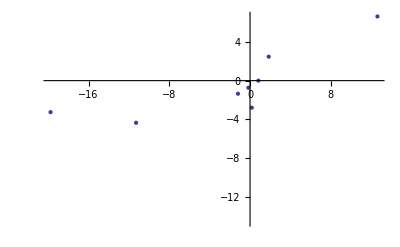

```mathematica
ListPlot[Table[{Re[n],Im[n]},{n,zeros[1000,.5+30I]}]]
```

```mathematica
Expand[N[zeta[100,3I,z,1]]]
```

1.+(5.76904+1.2356 ⅈ) z+(14.6072-0.934103 ⅈ) z^2+(8.3492-0.107725 ⅈ) z^3+(2.296-0.623888 ⅈ) z^4+(0.191317-0.0770772 ⅈ) z^5+(0.00496385-0.00740045 ⅈ) z^6

```mathematica
Clear[f,fr]
f[n_,0,s_,a_]:=1
fr[n_,s_]:=fr[n,s]=Sum[N[m^-s],{m,1,n}]
f[n_,1,s_,a_]:=f[n,1,s,a]=fr[Floor[n],s]-fr[a,s]
f[n_,k_,s_,a_]:=f[n,k,s,a]=N[Sum[Binomial[k,j] (m^-s)^j f[Floor[n/(m^j)],k-j,s, m],{j,1,k},{m,a+1,Floor[n^(1/k)]}]]
```

```mathematica
Timing[f[1000000,4,N[3+7I], 0]]
```

{14.414,1.00108+0.397512 ⅈ}

```mathematica
Clear[f]
f[n_,0,s_,a_]:=1
f[n_,1,s_,a_]:=f[n,1,s,a]=N[HarmonicNumber[n,s]]-N[HarmonicNumber[a,s]]
f[n_,k_,s_,a_]:=f[n,k,s,a]=N[Sum[Binomial[k,j] (N[m]^-s)^j f[Floor[n/(N[m]^j)],k-j,s,m],{j,1,k},{m,a+1.,Floor[N[n]^(1./k)]}]]
```

```mathematica
HarmonicNumber[10,I]//N
```

0.0418976-7.84548 ⅈ

```mathematica
N[Sum[ j^I,{j,1,10}]]
```

0.0418976+7.84548 ⅈ

```mathematica
Timing[f[1000000,4,N[3+7I], 0]]
```

{4.976,1.00108+0.397512 ⅈ}

```mathematica
Log[Zeta[s]]Integrate[Zeta[s]^z,z]
```

Zeta[s]^z

```mathematica
D[Zeta[s]^z,z]/Log[Zeta[s]]
```

Zeta[s]^z

```mathematica
D[Zeta[s]^z,z]/Zeta[s]^z
```

Log[Zeta[s]]

```mathematica
Zeta[s]^z/Integrate[Zeta[s]^z,z]
```

Log[Zeta[s]]

```mathematica
Clear[zeta]
Integrate[ zeta[100,0,z,1],z]
```

z+(214 z^2)/15+(16289 z^3)/1080+(331 z^4)/64+(611 z^5)/720+(67 z^6)/1440+z^7/720

```mathematica
Expand[D[ zeta[100,0,z,1],z]]
```

428/15+(16289 z)/180+(993 z^2)/16+(611 z^3)/36+(67 z^4)/48+(7 z^5)/120

```mathematica
Integrate[Zeta[s]^z,z]/Zeta[s]^z
```

1/Log[Zeta[s]]

```mathematica
Zeta[s]^z/D[Zeta[s]^z,z]
```

1/Log[Zeta[s]]

```mathematica
D[Zeta[s]^z,z]/Zeta[s]^z
```

Log[Zeta[s]]

```mathematica
Expand[Sum[ (zeta[j,0,-z,1]-zeta[j-1,0,-z,1]) D[ zeta[Floor[100/j],0,z,1],z],{j,1,100}]]
```

428/15

```mathematica
Expand[Sum[ (D[zeta[j,0,z,1]-zeta[j-1,0,z,1],z])  zeta[Floor[100/j],0,-z,1],{j,1,100}]]
```

428/15

```mathematica
Expand[Sum[Integrate[(zeta[j,0,z,1]-zeta[j-1,0,z,1]),z] zeta[Floor[100/j],0,-z,1],{j,1,100}]]
```

z-(214 z^2)/15+(16289 z^3)/1080-(331 z^4)/64+(611 z^5)/720-(67 z^6)/1440+z^7/720

```mathematica
D[Zeta[s]^z,{z,1}]/Zeta[s]^z
D[Zeta[s]^z,{z,2}]/Zeta[s]^z
D[Zeta[s]^z,{z,3}]/Zeta[s]^z
```

Log[Zeta[s]]

Log[Zeta[s]]^2

Log[Zeta[s]]^3

```mathematica
Zeta[s]^z/Integrate[Zeta[s]^z,z]
```

```mathematica
D[Zeta[s]^z,{z,3}]/D[Zeta[s]^z,{z,2}]
```

Log[Zeta[s]]

```mathematica
Expand[Sum[ (D[zeta[j,0,z,1]-zeta[j-1,0,z,1],{z,2}]) zeta[Floor[100/j],0,-z,1],{j,1,100}]]
```

16289/180

```mathematica
D[zeta[100,0,z,1],{z,2}]/.z->0
```

16289/180

```mathematica
Limit[(Zeta[s]^z-1)/z,z->0]
```

```mathematica
D[ Zeta[s]^z,{z,2}]/Zeta[s]^z
```

Log[Zeta[s]]^2

```mathematica
Log[Zeta[s]]
```

Log[Zeta[s]]

```mathematica
-D[N[Expand[Sum[ D[dzeta[j,s,z],s] zeta[100/j,s,-z,1],{j,1,100}]]/.s->1],z]
-D[N[Expand[Sum[ D[zeta[100/j,s,z,1],s] dzeta[j,s,-z],{j,1,100}]]/.s->1],z]
```

3.98562

3.98562

```mathematica
chebyshev[n_]:=Sum[MangoldtLambda[j],{j,2,n}]
dz[n_,z_,s_]:=(n^-s)Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[n]}];FI[n_]:=FactorInteger[n];FI[1]:={}
Dz[n_,z_,s_]:=Sum[dz[j,z,s],{j,1,n}]
Table[Chop[(-N[Sum[dz[j,-1,0](D[Dz[n/j,1,s],s]/.s->0),{j,1,n}]])],{n,10,100,10}]
Table[Chop[(-N[Sum[(D[Dz[n/j,1,s],s]/.s->0)dz[j,-1,0],{j,1,n}]])],{n,10,100,10}]
```

{7.83201,19.2657,28.4765,36.2146,49.4854,57.5332,66.5419,79.4645,89.4706,94.0453}

{7.83201,19.2657,28.4765,36.2146,49.4854,57.5332,66.5419,79.4645,89.4706,94.0453}

```mathematica
Table[Chop[(-N[Sum[dzeta[j,-1,0](D[zeta[n/j,s,1],s]/.s->0),{j,1,n}]])],{n,10,100,10}]
Table[Chop[(-N[Sum[(D[Dz[n/j,1,s],s]/.s->0)dzeta[j,-1,0],{j,1,n}]])],{n,10,100,10}]
```

```mathematica
Table[FullSimplify[(-D[D[zeta[n,s,z,1],z]/.z->0,s])-(-D[D[zeta[n-1,s,z,1],z]/.z->0,s])],{n,2,20}]//TableForm
```

2^-s Log[2]
3^-s Log[3]
4^-s Log[2]
5^-s Log[5]
0
7^-s Log[7]
8^-s Log[2]
9^-s Log[3]
0
11^-s Log[11]
0
13^-s Log[13]
0
0
16^-s Log[2]
17^-s Log[17]
0
19^-s Log[19]
0

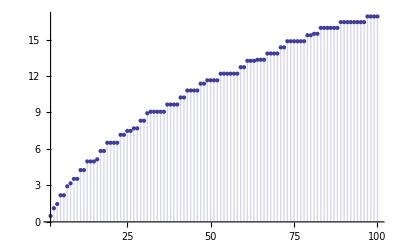

```mathematica
DiscretePlot[-N[D[D[zeta[n,s,z,1],z]/.z->0,s]]/.s->1/2,{n,2,100}]
```

```mathematica
Expand[pz[fe,100,z]]
```

1+(428 z)/15+(16289 z^2)/360+(331 z^3)/16+(611 z^4)/144+(67 z^5)/240+(7 z^6)/720

```mathematica
fe2[n_,s_] := (s-1)^-1 ( n/(n+1 )^s - (n-s)/n^s)
fe20[n_] := fe2[n,0]
```

```mathematica
Expand[pz[fe20,100,z]]
```

```mathematica
Sum[ fe2[n,2],{n,1,10}]
```

250868609/153679680

```mathematica
Sum[ j^-2,{j,1,10}]
```

1968329/1270080

```mathematica
Sum[ fe2[j,s],{j,1,Infinity}]
```

∑_(j=1)^∞ (j (1+j)^-s-j^-s (j-s))/(-1+s)

```mathematica
N[Integrate[ (x^(3-1)/(E^x-1)),{x,0,Log[10]}]]
```

1.17035

```mathematica
N[Sum[ j^-3,{j,1,10}]]
```

1.19753

```mathematica
zeta[100,1,1,1]
```

14466636279520351160221518043104131447711/2788815009188499086581352357412492142272

```mathematica
zeroh[n_,s_]:=List@@NRoots[zeta[n,s,z,1]==0,z][[All,2]]
```

```mathematica
Table[zeroh[n,1],{n,4,10}]//TableForm
```

-6.4207 | -1.24597 | 
-8.30318 | -0.963486 | 
-2.70299 | -1.26843 | 
-3.47442 | -0.986804 | 
-11.9371 | -4.07645 | -0.986414
-15.548 | -3.13336 | -0.985271
-21.4404 | -1.73867 | -1.28763

```mathematica
Sum[ BernoulliB[k]/k! (Zeta[s]-1) Log[Zeta[s]]^(k),{k,0,Infinity}]
```

Log[Zeta[s]]

```mathematica
Sum[ BernoulliB[k]/k!Sum[  D[zeta[100/j,0,z,1],{z,k}]/.z->0,{j,2,100}],{k,0,Log[2,100]}]
```

428/15

```mathematica
D[zeta[100,0,z,1],{z,-1}]/.z->0
```

D::dvar: Multiple derivative specifier {z, -1} does not have the form {variable, n}, where n is a non-negative machine integer.

D::dvar: Multiple derivative specifier {0, -1} does not have the form {variable, n}, where n is a non-negative machine integer.

∂_{0,-1} 1

```mathematica
Sum[ BernoulliB[k]/k!Sum[  D[zeta[100/j,0,z,1],{z,k-1}]/.z->0,{j,2,100}],{k,1,Log[2,100]}]+1/Sum[ BernoulliB[k]/k!Sum[  D[zeta[100/j,0,z,1],z]/.z->0,{j,2,100}],{k,0,0}]
```

-3138807413/88637760

```mathematica
Sum[ BernoulliB[k]/k! (Zeta[s]-1) D[Zeta[s]^z,{z,k}]/Zeta[s]^z,{k,0,Infinity}]
```

$Aborted

```mathematica
(D[Zeta[s]^z,z])/Zeta[s]^z
```

Log[Zeta[s]]

```mathematica
Residue[ ((Zeta'[s]/Zeta[s])) x^s s^(-1),{s,ZetaZero[1]}]
```

x^ZetaZero[1]/ZetaZero[1]

```mathematica
((D[Zeta[s]^z,z]/Zeta[s]^z)) x^s s^(-1)
```

(x^s Log[Zeta[s]])/s

```mathematica
((D[Zeta[s]^z,z]/Zeta[s]^z)) x^s s^(-1)
```

```mathematica
Log[Zeta[s]]^(3/2)
```

Log[Zeta[s]]^(3/2)

```mathematica
rr[]:=RandomReal[{-3,3}]+RandomReal[{-3,3}]I
zeta[n_,s_,z_,k_]:=1+((z+1)/k-1)Sum[zeta[n/j,s,z,k+1],{j,2,n}]
logzeta[n_,s_,k_]:=Limit[D[zeta[n,s,z,1],{z,k}],z->0]
Table[logzeta[n,a=rr[],k]-k! Residue[zeta[n,a,z,1]/z^(k+1),{z,0}],{n,1,50},{k,1,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
lgz[n_, k_] := Gamma[k+1] Residue[zeta[n,a,z,1]/z^(k+1),{z,0}]
```

```mathematica
Integrate[ Log[ Zeta[s]] Zeta[s]^z,z]
```

Zeta[s]^z

```mathematica
Integrate[ Zeta[s]^z,z]
```

Zeta[s]^z/Log[Zeta[s]]

```mathematica
Sum[ z^k/ (k!) Log[Log[Zeta[s]]]^k,{k,0,Infinity}]
```

Log[Zeta[s]]^z

```mathematica
1+Integrate[ Log[Zeta[s]] Zeta[s]^y,{y,0,z}]
```

Zeta[s]^z

```mathematica
Sum[ (-1)^(k+1)/k (Log[Zeta[s]]-1)^k,{k,1,Infinity}]
```

Log[Log[Zeta[s]]]

```mathematica
Series[ Log[Log[x+1]],{x,0,10}]
```

Log[x]-x/2+(5 x^2)/24-x^3/8+(251 x^4)/2880-(19 x^5)/288+(19087 x^6)/362880-(751 x^7)/17280+(1070017 x^8)/29030400-(2857 x^9)/89600+(26842253 x^10)/958003200+O[x]^11

```mathematica
Series[ Log[x-1],{x,0,10}]
```

ⅈ π-x-x^2/2-x^3/3-x^4/4-x^5/5-x^6/6-x^7/7-x^8/8-x^9/9-x^10/10+O[x]^11

```mathematica
Sum[ (-1)^(k) Binomial[z,k] x^k,{k,0,Infinity}]
```

(1-x)^z

```mathematica
HurwitzZeta[s,2]
```

-1+Zeta[s]

```mathematica
Sum[ 1/(q+j)^s,{j,1,Infinity}]^2
```

HurwitzZeta[s,1+q]^2

```mathematica
(1/3+1/4+1/5+1/6)(1/3+1/4+1/5+1/6)
```

```mathematica
dd[n_,s_,1,q_] := If[ n >= q,n^-s,0]
dd[n_, s_, k_,q_] := dd[n,s,k,q]=Sum[If[ dd[a,s,1,q]==0,0, dd[a,s,1,q] dd[n/a,s,k-1,q]],{a,Divisors[n]}]
```

```mathematica
Table[dd[16,2,3,n],{n,1,10}]
```

{15/256,3/256,0,0,0,0,0,0,0,0}

```mathematica
N[Sum[ dd[n,2,2,7],{n,1,100000}]]
```

0.0234884

```mathematica
N[Zeta[2,7]^2]
```

0.0235761